```mathematica
(*Introduction*)



!X    (*Not[x]*)
x!     (*Factorial[x]*)
x+y+z     (*Plus[x,y,z]*)
{x,y,z}     (*List[x,y,z]*)
x/:y=z      (*TagSet[x,y,z]*)
OverHat[x](*Makes xhat*)
```

!X

x!

x+y+z

{x,y,z}

TagSet::tagnf: Tag x not found in y.

z

x̂

```mathematica
{FullForm[a*b+c],FullForm[a+b*c]}
```

{Plus[Times[a,b],c],Plus[a,Times[b,c]]}

```mathematica
a*b+c//f
```

f[a b+c]

```mathematica
f@a*b+c
```

c+b f[a]

```mathematica
FullForm[a*(b+c)]
```

Times[a,Plus[b,c]]

```mathematica
(*http://reference.wolfram.com/mathematica/tutorial/OperatorInputForms.html is the website to go over precedent documentation*)
```

```mathematica
∀_x∃_y x⊗y≻y ∧ m != 0 ⇒ n ⧐̸ m;
FullForm[%]
```

Implies[And[ForAll[x,Exists[y,Succeeds[CircleTimes[x,y],y]]],Unequal[m,0]],NotRightTriangleBar[n,m]]

```mathematica
{x->#^2&,(x->#^2)&,x->(#^2&)}
```

{x→#1^2&,x→#1^2&,x→(#1^2&)}

```mathematica
{x->#^2&,(x->#^2)&,(x->#^2&)} (*Note the difference from the line of code above it, the third part requires explicit parentheses*)
```

{x→#1^2&,x→#1^2&,x→#1^2&}

```mathematica
FullForm[f^g^h^i]
```

Power[f,Power[g,Power[h,i]]]

```mathematica
$MaxNumber
```

1.23343371298165×10^323228458

```mathematica
(*What do infix, matchfix, compound, and overfix mean?*)
```

```mathematica
∫k[x] ⅆx//FullForm (*Standard Integral*)
```

Integrate[k[x],x]

```mathematica
∫(a[x]+b[x]) ⅆx+c[x]  (*using parentheses to specify what to integrate*)
```

4[x]+∫(2[x]+3[x])ⅆx

```mathematica
x^(a+b)
```

x^5

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
∑_(n=1)^∞ 1/n^s
```

Zeta[s]

```mathematica
(*Use parentheses to group stuff to determine the precedence of operations*)
1+2/3
(1+2)/3
```

5/3

1

```mathematica
(* the use of curley braces represents a list and is a colleciton of items referred to as the elements*)
{1,b,2,3,3 x==12,Sqrt[9+y],"hello"}
{1,1,{3,4,5},{3,2}}
```

{1,3,2,3,3 x==12,√(9+y),hello}

{1,1,{3,4,5},{3,2}}

```mathematica
(*Square brackets are use to enclose the arguments of functions*)
Range[10]
Sin[2]
N[Sin[2]]
```

{1,2,3,4,5,6,7,8,9,10}

Sin[2]

0.909297

```mathematica
(*Double brackets are used for the Part functions to get the parts of lists*)
V=Range[10]^2
V[[3]]
```

{1,4,9,16,25,36,49,64,81,100}

9

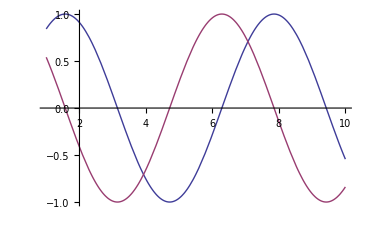

```mathematica
Plot[{Sin[x], Cos[x]}, {x, 1, 10}]
```

```mathematica
(*Head['some expression'] gives the head of some expression*)
Head[f[j,k]]
```

f

```mathematica
Head[j+k+L]
```

Plus

```mathematica
Head[{j,k,L}]
```

List

```mathematica
Head[45]
```

Integer

```mathematica
Head[x]
```

Symbol

```mathematica
(*Things like Factor['some expression'] are commands that make something happen*)
Factor[x^6-1]
```

(-1+x) (1+x) (1-x+x^2) (1+x+x^2)

```mathematica
(*(term) parentheses for grouping
f[x] square brackets for functions
{a,b,c} curly braces for lists
v[[i]] double brackets for indexing (Part[v,i])*)
```

```mathematica
(*Symbolic Manipulation*)
```

```mathematica
xy+2x^2y+y^2x^2-2xy
```

-xy+2 x^2 y+x^2 y^2

```mathematica
(x+2y+1)(x-2)^2
```

(-2+x)^2 (1+x+2 y)

```mathematica
Expand[%]
```

4-3 x^2+x^3+8 y-8 x y+2 x^2 y

```mathematica
Factor[%]
```

(-2+x)^2 (1+x+2 y)

```mathematica
Sqrt[2]/9801(4n)!(1103+26390n)/(n!^4 396^(4n))
```

(2^(1/2-8 n) 99^(-2-4 n) (1103+26390 n) (4 n)!)/(n!)^4

```mathematica
1+2x /. x->3
```

7

```mathematica
1+x+x^2 /. x->2-y
```

3+(2-y)^2-y

```mathematica
Expand[%]
```

7-5 y+y^2

```mathematica
(*Transformation Rules*)
```

```mathematica
x-> 3+y
```

x→3+y

```mathematica
(x+y)(x-y)^2 /. %
```

9 (3+2 y)

```mathematica
(x+y)(x-y)^2 /. {x->3, y ->1-a}
```

(4-a) (2+a)^2

```mathematica
(*Assigning a value to a variable early on will result in it getting filled into it later*)
```

```mathematica
x = 3
```

3

```mathematica
x^2-1
```

8

```mathematica
x = 1+a
```

1+a

```mathematica
x^2-1
```

-1+(1+a)^2

```mathematica
(*Use x=value to assign a value to x that will ALWAYS be used.
Use x=. to remove all values for x*)
```

```mathematica
x=.
```

```mathematica
x^2-1
```

-1+x^2

```mathematica
x=.
```

```mathematica
x
```

x

SetDelayed::write: Tag Times in a\ assigns\ the\ This\ to\ value\ symbol . 2^1/2 - 8\ n\ 99^-2 - 4\ n\ (1103 + 26390\ n)\ (4\ n) !/(n !)^4 is Protected.

```mathematica
(*Transforming Algebraic Experessions*)
```

```mathematica
Expand(1+x)^2
```

Expand (1+x)^2

```mathematica
Expand[(1+x)^2]
```

1+2 x+x^2

```mathematica
Factor[%]
```

(1+x)^2

```mathematica
Expand[(1+x+3y)^5] (*Easy way to make a complicated expression*)
```

1+5 x+10 x^2+10 x^3+5 x^4+x^5+15 y+60 x y+90 x^2 y+60 x^3 y+15 x^4 y+90 y^2+270 x y^2+270 x^2 y^2+90 x^3 y^2+270 y^3+540 x y^3+270 x^2 y^3+405 y^4+405 x y^4+243 y^5

```mathematica
(*Simplifying Algebraic Expressions*)
```

```mathematica
(*Use the Simplify[] and FullSimplify[] Expressions
Simplify uses basic algebra to simplify
FullSimplify uses a wide range of transformations*)
```

```mathematica
Simplify[x^2+2x+1]
```

(1+x)^2

```mathematica
-1/(4(1-x))-1/(4(1+x))-1/(2(1+x^2))
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Integrate[1/(x^4-1), x]
```

-ArcTan[x]/2+1/4 Log[1-x]-1/4 Log[1+x]

```mathematica
D[%,x] (*Should return the thing we integrated, but doesn't so we have to simplify*)
```

-1/(4 (1-x))-1/(4 (1+x))-1/(2 (1+x^2))

```mathematica
Simplify[%]
```

1/(-1+x^4)

```mathematica
Simplify[Gamma[x]Gamma[1-x]]
```

Gamma[1-x] Gamma[x]

```mathematica
FullSimplify[Gamma[x]Gamma[1-x]]
```

π Csc[π x]

```mathematica
(*Calculus
D[f,x] is the partial derivative in regards to x
D[f,x,y,...] does multiple partial derivatives
D[f,{x,n}] does the nth derivative
D[f,x,Nononstants->{v1,v2,...}] does partial in regards to x with the v's depending on x*)
```

```mathematica
D[x^n, x]
```

n x^(-1+n)

```mathematica
D[x^n, {x,3}]
```

(-2+n) (-1+n) n x^(-3+n)

```mathematica
D[x[1]^2+x[2]^2, x[1]]
```

2 x[1]

```mathematica
D[x^2+y^2, x]
```

2 x

```mathematica
D[x^2+y^2, {{x,y}}] (*Gives the gradient*)
```

{2 x,2 y}

```mathematica
(*Integration*)
```

```mathematica
Integrate[x^n,x]
```

x^(1+n)/(1+n)

```mathematica
(*Integrate[f,x] does the indefinite integral
Integrate[f,x,y] does the multiple integral with dx on the inside and then dy
Integrate[f, {X,Xmin,Xmax}] integrates from Xmin to Xmax
Integrate[f, {X, Xmin, Xmax},{Y, Ymin, Ymax}] does a double integral along the bounds*)
```

```mathematica
Integrate[Exp^x, {x, 0, 4}]
```

(-1+Exp^4)/Log[Exp]

```mathematica
Integrate[Exp[-x^2], {x, 0, Infinity}]
```

(√π)/2

```mathematica
Integrate[x^2+y^2, {x,0,1},{y,0,x}]
```

1/3

```mathematica
(*Indefinite Integrals*)
```

```mathematica
Integrate[x^2, x]
```

x^3/3

```mathematica
D[%+c,x]
```

x^2

```mathematica
(*Integrate is like an inverse of the partial differentiation function D*)
```

```mathematica
Integrate[a x^2, x] (*Assumes that 'a' is independant of x*)
```

(a x^3)/3

```mathematica
(*Differential Equations*)
```

```mathematica
(*Use DSolve to solve a DE.
You will usually want to solve for y though, not y in terms of x (y[x]) because this is the form that you can punch back into you DE and get a value because mathematica will differentiate your y but not y[x]*)
```

```mathematica
DSolve[y'[x]+y[x]==1,y[x],x]
```

{{y[x]→1+ⅇ^-x C[1]}}

```mathematica
(*Lets say our DE is the following*)
y[x]+2y'[x]+y[0] /. y[x]->1+Exp^(-x) C[1]
```

```mathematica
1+Exp^-x C[1]+y[0]+2 y'[x] (*as you see, it didn't differentiate y[x] to get y'[x]
```

```mathematica
(*could have also used % after the /. and gotten same result, because its saying to put in your last output*)
```

```mathematica
DSolve[y'[x]+y[x]==1,y,x]
```

{{y→Function[{x},1+ⅇ^-x C[1]]}}

```mathematica
y[x]+2y'[x]+y[0] /. %
```

```mathematica
{2+C[1]-ⅇ^-x C[1]} (*See it actually differentiated out y and plugged in and then simplified, FUCKING AWESOME!*)
```

{2+C[1]-ⅇ^-x C[1]}

```mathematica
(*Plotting*)
Plot[Sin[x], {x, 0, 10}]
```

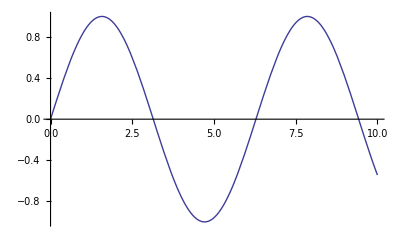

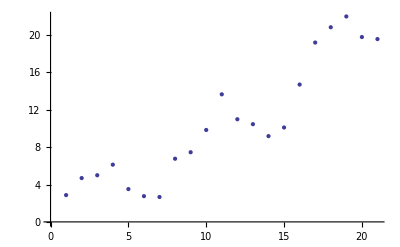

```mathematica
datapts = Table[x+RandomReal[{-4,4}],{x,0,20}];
ListPlot[datapts]
```

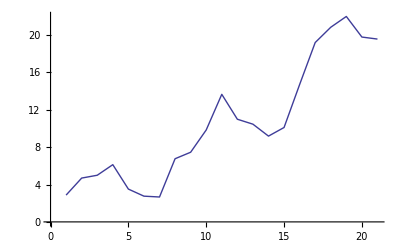

```mathematica
ListLinePlot[datapts]
```

```mathematica
Plot3D[Sin[x] Cos[y], {x,0,5}, {y,1,10}]
```

-Graphics3D-

```mathematica
GraphicsGrid[{{Plot3D[Sin[x] Cos[y], {x,0,5}, {y,1,10}], Plot3D[Sin[x] Cos[y], {x,0,5}, {y,1,10}, ColorFunction->(Hue[#3] &), MeshFunctions-> (#3 &), Boxed-> False, Axes->False]}}]
```

-Graphics-

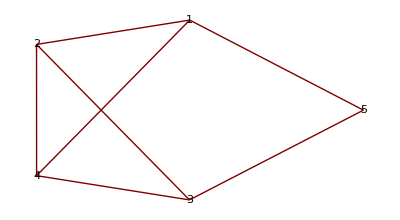

```mathematica
GraphPlot[{1->2,1->4,2->4,3->4,3->2,3->5,5->1}, VertexLabeling->True]
```

```mathematica
(*Plotting Functions of One Variable*)
```

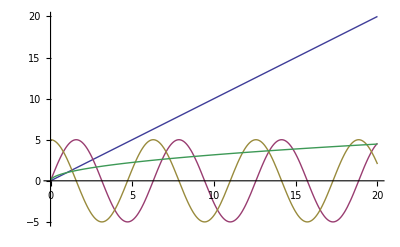

```mathematica
Plot[{x,5 Sin[x],5 Cos[x],Sqrt[x]},{x,0, 20}]
```

```mathematica
E
```

ⅇ

```mathematica
N[ⅇ]
```

2.71828

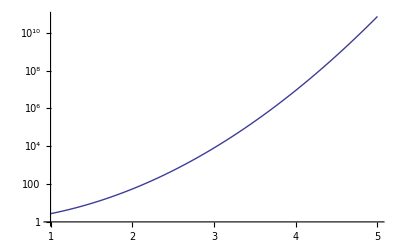

```mathematica
LogPlot[E^x^2, {x,1,5}]
```

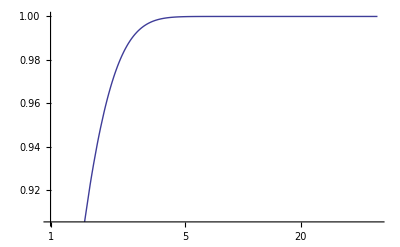

```mathematica
LogLinearPlot[Tanh[x], {x,1,50}]
```

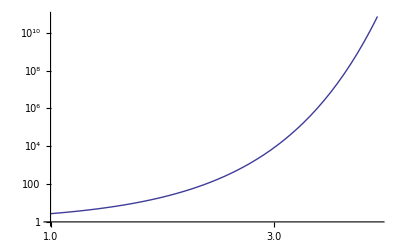

```mathematica
LogLogPlot[E^x^2, {x,1,5}]
```

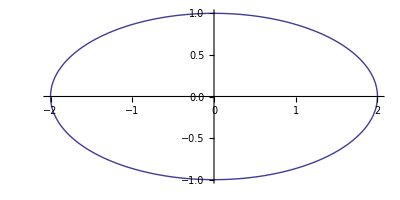

```mathematica
ParametricPlot[{2 Sin[t],Cos[t]}, {t,0, 2 Pi}]
```

```mathematica
ParametricPlot3D[{5 Cos[t], 5 Sin[t], t+Sin[t]}, {t, -4Pi, 4 Pi}]
```

-Graphics3D-

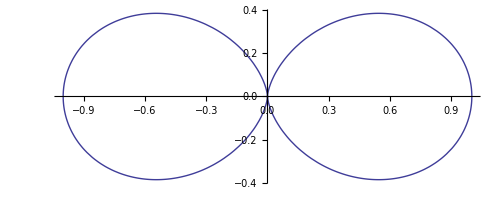

```mathematica
PolarPlot[Cos[t]^2, {t,0,2 Pi}]
```

```mathematica
Plot3D[x^3+x y^2+y==0, {x,-1,1}, {y,-10,10}]
```

-Graphics3D-

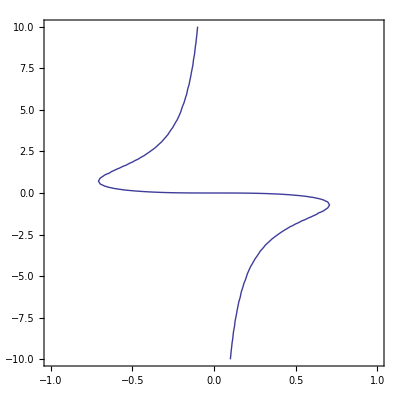

```mathematica
ContourPlot[x^3+x y^2+y==0, {x,-1,1}, {y,-10,10}]
```

```mathematica
(*Plotting the Reslts of NDSolve
NDSolve solves a DE numerically*)
```

```mathematica
ode1 = {y''[x]+Sin[y[x]]==0, y[0]==2, y'[0]==1};
sol = NDSolve[ode1,y,{x,-10,10}]
```

{{y→InterpolatingFunction[{{-10.,10.}},<>]}}

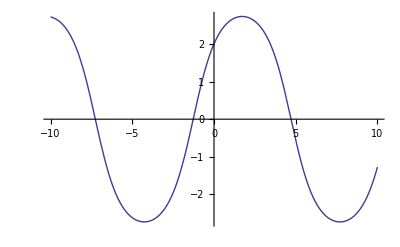

```mathematica
Plot[y[x] /. sol, {x,-10,10}]
```

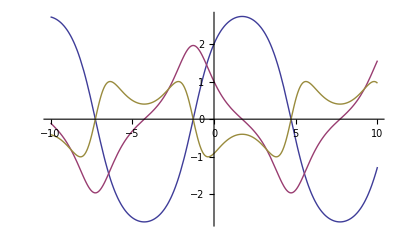

```mathematica
(*If we want to plot the solutions along with its derivatives, and see them in different colors, use Evaluate around what you want to plot*)
Plot[Evaluate[{y[x], y'[x], y''[x]} /. sol], {x, -10, 10}]
```

```mathematica
wws = NDSolve[{D[u[t,x], t,t] == D[u[t,x], x,x] + (1 - u[t, x]^2) (1 + 2 u[t, x]), u[0, x] == E^-x^2, 
Derivative[1,0][u][0, x] == 0, u[t, -10] == u[t, 10]}, 
  u, {t, 0, 10}, {x, -10, 10}]
```

{{u→InterpolatingFunction[{{0.,10.},{-10.,10.}},<>]}}

```mathematica
Plot3D[u[t,x] /. wws, {t, 0, 10}, {x,-10, 10}]
```

-Graphics3D-

```mathematica
plots = Table[Plot[u[t,x] /. wws, {x,-10,10}, PlotRange->{-2,2}], {t,0, 10, 0.25}];
ListAnimate[plots]
```

```mathematica
(*MANIPULATE*)
Table
```

```mathematica
Table (*Has useful documantation, manipulate is much like table (oddly enough)
Uses the form of (variable, min, max)*)
```

```mathematica
Table[n,{n,1,20}]
Manipulate[n,{n,1,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Manipulate[Plot[Sin[n x], {x,0, 2 Pi}], {n,1,20}]
```

```mathematica
Manipulate[Plot[Sin[n x], {x,0, 2 Pi}], {n,1,20, Appearance->"Labeled"}] (*Now we see what value n is at*)
```

```mathematica
Manipulate[ParametricPlot3D[{5 Cos[x t], 5 Sin[x t], t+Sin[t]},{t, -4Pi, 4 Pi}], {x,1,100,Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x], {x, 0, 2 Pi}], {n1, 1, 20, Appearance->"Labeled"}, {n2, 1, 20, Appearance->"Labeled"}]
```

```mathematica
Manipulate[Plot[a1 Sin[n1 (x+p1)]+a2 Sin[n2 (x+p2)],{x,0,2 Pi},PlotRange->2],{n1,1,20},{a1,0,1},{p1,0,2 Pi},{n2,1,20},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[Expand[(α+β)^n], {n,1,200,1}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x], {x, 0, 2 Pi}, Filling->filling, PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None, Axis, Top, Bottom,Automatic}}]
```

```mathematica
Manipulate[Plot[Sin[n1 x]+Sin[n2 x],{x,0,2 Pi},Filling->filling,PlotRange->2],{n1,1,20},{n2,1,20},{filling,{None,Axis,Top,Bottom,Automatic,1,0.5,0,-0.5,-1},ControlType->Manipulator}]
```

```mathematica
(*Fun Demo*)
Manipulate[ParametricPlot[{a1 Sin[n1 (x+p1)],a2 Cos[n2 (x+p2)]},{x,0,20 Pi},PlotRange->1,PerformanceGoal->"Quality"],{n1,1,4},{a1,0,1},{p1,0,2 Pi},{n2,1,4},{a2,0,1},{p2,0,2 Pi}]
```

```mathematica
Manipulate[Graphics[{PointSize[0.1],Point[pt]},PlotRange->1],{pt,  {-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[{Line[Table[{{Cos[t],Sin[t]},pt},{t,2. Pi/n,2. Pi,2. Pi/n}]]},PlotRange->1],{{n,30},1,200,1},{pt,{-1,-1},{1,1}}]
```

```mathematica
Manipulate[Graphics[{Line[Table[{{Cos[t],Sin[t]},pt},{t,2. Pi/n,2. Pi,2. Pi/n}]]},PlotRange->1],{{n,30},1,200,1}, {{pt, {0,0}}, Locator}]
```

```mathematica
Manipulate[Graphics[Polygon[{pt1,pt2,pt3}],PlotRange->1],{{pt1,{0,0}},Locator},{{pt2,{0,1}},Locator},{{pt3,{1,0}},Locator}]
```